```mathematica
ResourceFunction["StemLeafPlot"][{1.2,2.5,4.1,1.6,3.8,2.6,2.9}]
```

Stem | Leaves
1 | 26
2 | 569
3 | 8
4 | 1
Stem units: 1

```mathematica
data={76,74,82,96,66,76,78,72,52,68,86,84,62,76,78,92,82,74,88,84};
```

```mathematica
ResourceFunction["StemLeafPlot"][data]
```

Stem | Leaves
5 | 2
6 | 268
7 | 24466688
8 | 224468
9 | 26
Stem units: 10

```mathematica
ResourceFunction["StemLeafPlot"][data,"IncludeStemUnits"->False]
```

Stem | Leaves
5 | 2
6 | 268
7 | 24466688
8 | 224468
9 | 26

```mathematica
ResourceFunction["StemLeafPlot"][data,"IncludeStemUnits"->False,"IncludeStemCounts"->True]
```

Stem | Leaves | Counts
5 | 2 | 1
6 | 268 | 3
7 | 24466688 | 8
8 | 224468 | 6
9 | 26 | 2

```mathematica
expandeddata=AppendTo[data,36]
```

{76,74,82,96,66,76,78,72,52,68,86,84,62,76,78,92,82,74,88,84,36}

```mathematica
ResourceFunction["StemLeafPlot"][expandeddata]
```

Stem | Leaves
3 | 6
5 | 2
6 | 268
7 | 24466688
8 | 224468
9 | 26
Stem units: 10

```mathematica
distribution=EstimatedDistribution[expandeddata,NormalDistribution[a,b]]
```

NormalDistribution[75.3333,13.1993]

```mathematica
StandardDeviation[distribution]
```

13.1993

```mathematica
Median[distribution]
```

75.3333

```mathematica
Mean[distribution]
```

75.3333

```mathematica
Kurtosis[distribution]
```

3

```mathematica
Probability[x<=36,x\[Distributed]EstimatedDistribution[expandeddata,NormalDistribution[a,b]]]
```

0.00144148

```mathematica
Probability[x<=52,x\[Distributed]EstimatedDistribution[expandeddata,NormalDistribution[a,b]]]
```

0.0385499

```mathematica
Probability[x>=96,x\[Distributed]EstimatedDistribution[expandeddata,NormalDistribution[a,b]]]
```

0.0587052

```mathematica
traveldata={1,18,4,9,9,7,7,16,11,4,3,4,1,8,12,15,8,9,4,13,4,6,10,7,6,1,11,1,3,8,14,5,4,2,5,2,10,6,2,14,2,17,5};
```

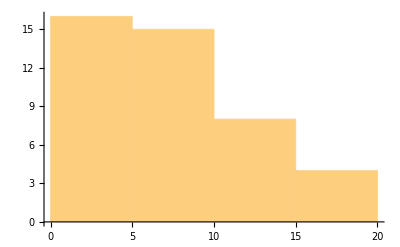

```mathematica
Histogram[traveldata]
```

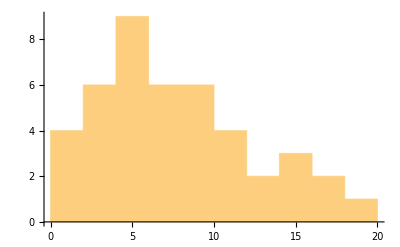

```mathematica
Histogram[traveldata,"Sturges"]
```

```mathematica
Histogram[traveldata,"Scott"]
```

-Graphics-

```mathematica
Histogram[traveldata,"FreedmanDiaconis"]
```

-Graphics-

```mathematica
Length[traveldata]
```

43

```mathematica
√Length[traveldata]
```

√43

```mathematica
N[√Length[traveldata]]
```

6.55744

```mathematica
Histogram[traveldata,"Knuth"]
```

-Graphics-

```mathematica
Histogram[traveldata,"Wand"]
```

-Graphics-

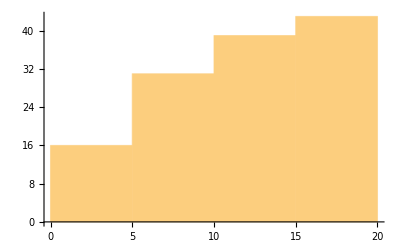

```mathematica
Histogram[traveldata,"Wand","CumulativeCount"]
```

```mathematica
Min[traveldata]
```

1

```mathematica
Max[traveldata]
```

18

```mathematica
Histogram[traveldata,ChartElementFunction->ChartElementDataFunction["Rectangle","RoundingRadius"->Offset[0]]]
```

-Graphics-

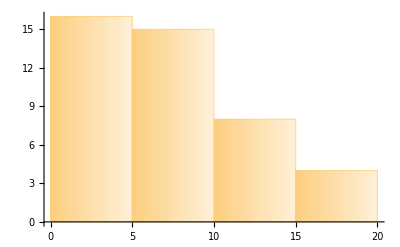

```mathematica
Histogram[traveldata,ChartElementFunction->"FadingRectangle"]
```

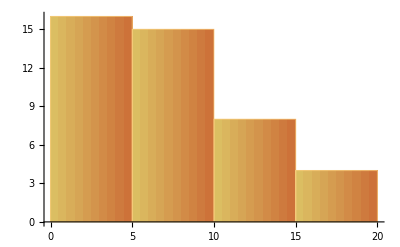

```mathematica
Histogram[traveldata,ChartElementFunction->ChartElementDataFunction["GradientRectangle","ColorScheme"->{RGBColor[0.863, 0.762, 0.395],RGBColor[0.8567, 0.7287, 0.3771],RGBColor[0.8504, 0.6954, 0.3592],RGBColor[0.8441, 0.6621, 0.3413],RGBColor[0.8378, 0.6288, 0.3234],RGBColor[0.8315, 0.5955, 0.3055],RGBColor[0.8252, 0.5621999999999999, 0.28759999999999997],RGBColor[0.8189000000000001, 0.5288999999999999, 0.2697],RGBColor[0.8126, 0.4956, 0.25179999999999997],RGBColor[0.8063, 0.4623, 0.2339],RGBColor[0.8, 0.429, 0.216]},"GradientOrigin"->Automatic]]
```

```mathematica
17./6
```

2.83333

```mathematica
BinCounts[traveldata]
```

{0,4,4,2,6,3,3,3,3,3,2,2,1,1,2,1,1,1,1}

```mathematica
BinCounts[traveldata,3]
```

{8,11,9,7,4,3,1}

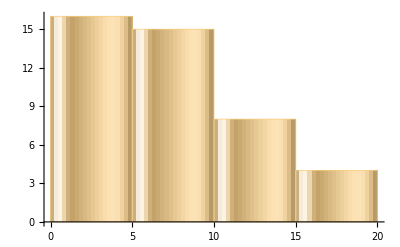

```mathematica
Histogram[traveldata,ChartElementFunction->"GlassRectangle"]
```

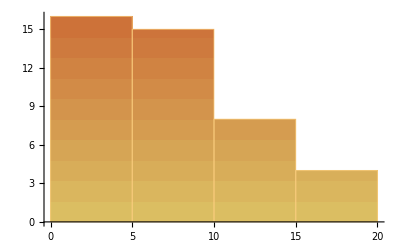

```mathematica
Histogram[traveldata,ChartElementFunction->ChartElementDataFunction["GradientScaleRectangle","ColorScheme"->{RGBColor[0.863, 0.762, 0.395],RGBColor[0.8567, 0.7287, 0.3771],RGBColor[0.8504, 0.6954, 0.3592],RGBColor[0.8441, 0.6621, 0.3413],RGBColor[0.8378, 0.6288, 0.3234],RGBColor[0.8315, 0.5955, 0.3055],RGBColor[0.8252, 0.5621999999999999, 0.28759999999999997],RGBColor[0.8189000000000001, 0.5288999999999999, 0.2697],RGBColor[0.8126, 0.4956, 0.25179999999999997],RGBColor[0.8063, 0.4623, 0.2339],RGBColor[0.8, 0.429, 0.216]}]]
```

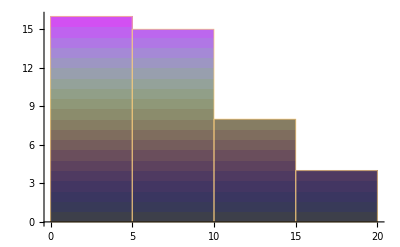

```mathematica
Histogram[traveldata,ChartElementFunction->ChartElementDataFunction["GradientScaleRectangle","ColorScheme"->"AuroraColors"]]
```

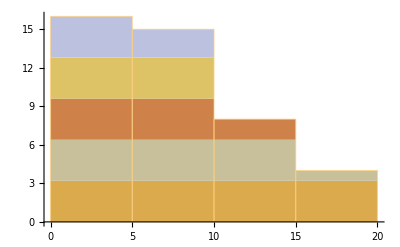

```mathematica
Histogram[traveldata,ChartElementFunction->"SegmentScaleRectangle"]
```

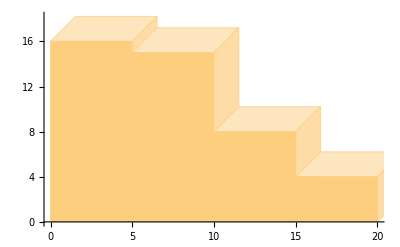

```mathematica
Histogram[traveldata,ChartElementFunction->"ObliqueRectangle"]
```

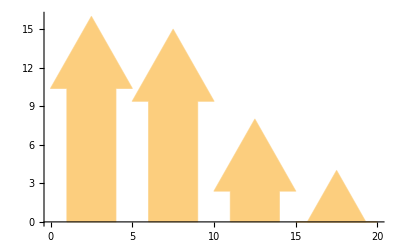

```mathematica
Histogram[traveldata,ChartElementFunction->"ArrowRectangle"]
```

```mathematica
Histogram[traveldata,ChartElementFunction->ChartElementDataFunction["Rectangle","RoundingRadius"->Offset[0]]]
```

-Graphics-

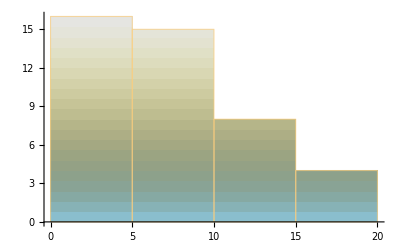

```mathematica
Histogram[traveldata,ChartElementFunction->ChartElementDataFunction["GradientScaleRectangle","ColorScheme"->"LightTerrain"]]
```

```mathematica
EstimatedDistribution[traveldata,NormalDistribution[a,b]]
```

NormalDistribution[7.16279,4.66022]

```mathematica
Commonest[traveldata]
```

{4}